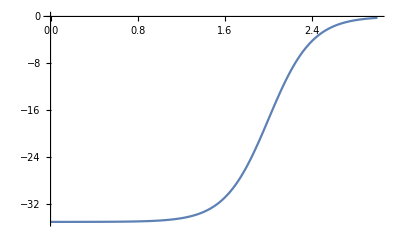

```mathematica
Subscript[m, N]=940;ℏc=197.327;
V0=35;R=2;a=0.2;μ=8/9 Subscript[m, N];
rmax=3.0;dr=0.01;
rlist=Range[0,rmax,dr];
n=Length[rlist];
V[r_]:=-V0/(1+Exp[(r-R)/a]);
Vmat=DiagonalMatrix[V[rlist]];
ListLinePlot[V[rlist],DataRange->{0,rmax}]
```

```mathematica
(*calculate Hamiltonian matrix and eigensystem*)
one[n_,d_]:=
DiagonalMatrix[1+0Range[n-Abs[d]],d];
H0=Vmat+-ℏc^2/(2 μ) 1/dr^2(one[n,-1]-2 one[n,0]+one[n,1]);
k[En_]:=Sqrt[(2μ En)/ℏc^2];
B[En_,δ_]:=1-dr Cot[k[En] rmax+δ] k[En];
Hnew[En_,δ_]:=(H=H0;H[[n,n]]=Vmat[[n,n]]+-ℏc^2/(2 μ) 1/dr^2(-2+B[En,δ]);H)

eigenv[{En_,i_,δ_}]:=({eval,evec}=Eigensystem[Hnew[En,δ]];{eval[[-i]],i})
```

```mathematica
En=10;
```

```mathematica
(*phase=Table[{eigenv[{En,1,x}][[1]],x},{x,0,Pi,0.01}];*)
```

```mathematica
NSolve[eigenv[{En,1,x}]==En,x]
```

```mathematica
FindRoot[eigenv[{En,1,δ}][[1]]==En,{δ,0,0,Pi},WorkingPrecision->2]
```

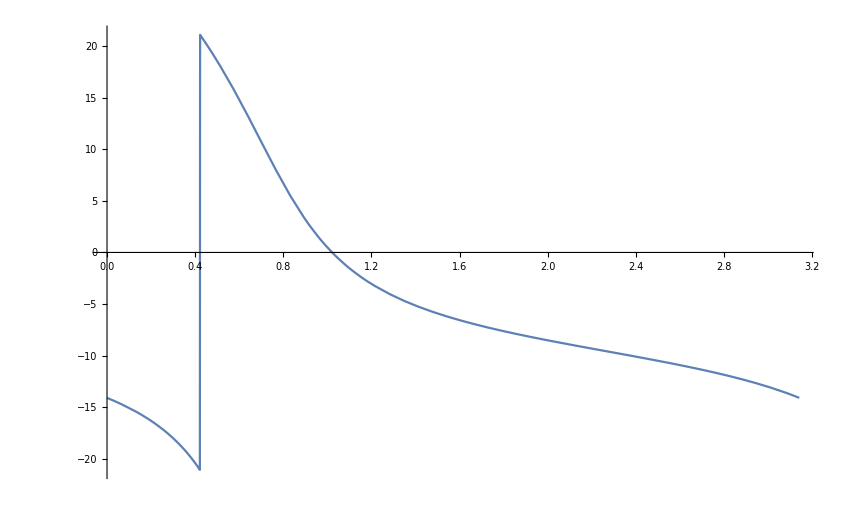

```mathematica
Plot[eigenv[{En,1,x}][[1]],{x,0,Pi}]
```

```mathematica
eigenv[{10,1,0.7172958}]
```

{10.0008,1}

```mathematica
En
```

10

```mathematica
δ=0.7172958
```

0.717296

```mathematica
{eval,evec}=Eigensystem[Hnew[En,δ]];
```

```mathematica
wave[En_,r_,δ_]:=Sin[k[En] r+δ]
const[i_]:=evec[[-i,-1]]/wave[En,rmax,δ]
```

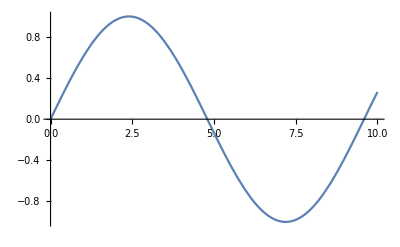

```mathematica
Plot[wave[10,r,0],{r,0,10}]
```

```mathematica
const[1]
```

0.164727

```mathematica
Manipulate[ListLinePlot[{Transpose[{rlist,Abs[evec⟦-i⟧]}],Transpose[{Range[rmax,20,dr],const[i] Abs[wave[eval[[-i]],Range[rmax,20,dr],δ]]}]},PlotRange->All],{i,1,n,1}]
```

```mathematica
eval[[-4]]
```

266.329